```mathematica
vomega={0,0,omega};
vv={vx,vy,0};
Manipulate[Graphics3D[{{Red,Arrow[{{0,0,0},2m{0,0,omega} ×{vx,vy,0}}]},Arrow[{{0,0,0},{vx,vy,0}}]},PlotRange->{{-6,6},{-6,6},{-1,1}},Axes->True,BaseStyle->Arrowheads[Medium]],{vx,-2,2},{vy,-2,2},{omega,-1,1},{m,-1,1}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

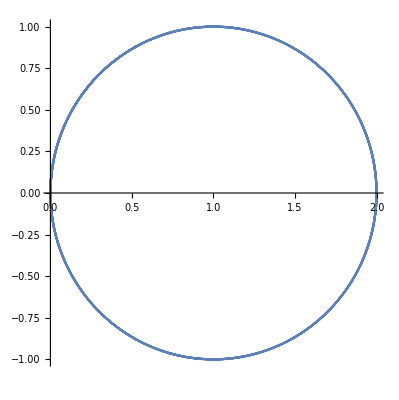

```mathematica
Clear[x,y,t,eqn,boun,solv]
eqn={x''[t]==y'[t],y''[t]==-x'[t]};
boun={x[0]==0,y[0]==0,x'[0]==0,y'[0]==1};
solv=NDSolve[{eqn,boun},{x,y},{t,0,20}]
ParametricPlot[Evaluate[{x[t],y[t]}/.solv],{t,0,20}]
```

```mathematica
Manipulate[VectorPlot3D[2{0,0,omega} ×{vx,vy,0},{x,-5,5},{y,-5,5},{z,0,0.1}],{{vx,1},-2,2},{{vy,1},-2,2},{omega,-2,2}]
```

```mathematica
{1,0}.{2,2}
{0,0,2}×{1,0,3}
```

{2 •,0}

{0,2,0}